## Madgraph

```mathematica
(*THIS NOTEBOOK RUNS A SINGLE SET OF PARAMETERS THROUGH PYTHIA + (optionally) BOOST FOR INSPECTION OF THE SPECTRUM*)
If[$Notebooks==True,SetDirectory[NotebookDirectory[]],SetDirectory[Directory[]]];

nevents=1000;
minDP=0.2;
maxDP=0.5;
pointsDP=6;
DPmasstab=Table[10.^lmA,{lmA,Log10[minDP],Log10[maxDP],(Log10[maxDP]-Log10[minDP])/(pointsDP-1)}]
DMmass=100000.;(*DM mass to scan over in boosting*)
(*These are parameters to be used in the MG5 scan -- they mostly don't matter for the model independent case*)
MGϵ=1. 10^-5;(*Mixing parameter between photon and dark photon -- doesn't really matter for the model independent scan here*)
MGαχ=0.024/1000. DMmass;(*Dark fine structure constant -- also doesn't matter here*)
MGmχ=DMmass;(*DM mass -- only need it big enough to avoid the DP decaying into them*)

hawcbins={{0.5,1.6,2.2 10^-12},{1.6,5.0,8.8 10^-13},{5.0,15.7,2.8 10^-13},{15.7,50,8.1 10^-14},{50,158,6.3 10^-14}};(*Start of bin (left edge) and flux limit in TeV and TeV cm^2 s^-1 respectively*)

(*fixedform is what makes the numbers nice to print to a file*)
StringPadLeft["",1];(*this must be evaluated first for no evident reason*)fixedform[numd_,data_]:=Module[{ef},ef[s_String/;StringTake[s,1]=="-"]:="-"<>StringPadLeft[StringTake[s,{2,-1}],2,"0"];
ef[s_String]:="+"<>StringPadLeft[s,2,"0"];
NumberForm[data,{numd,numd},ExponentFunction->(#&),NumberSigns->{"-"," "},NumberFormat:>(Row[{StringPadRight[#1,numd+2,"0"],"E",ef[#3]}]&)]]
$mg5outputfile = "DPdvb";
$widthsfile="DPwidths";
$inputfile="DPanninput";
$mg5runfile="DPmg5run";
$pythiaoutputfile="DPpythiaoutput";
$pythonoutputfile="DPpythonoutput";
$perannspecfile="DPperannspec";
$boostspecfile="DPboostspec";
$debugfile = "debug"<>$mg5outputfile;
talpha="thermal";
If[FileExistsQ[$debugfile],DeleteFile[$debugfile]];
```

{0.2,0.240225,0.28854,0.346572,0.416277,0.5}

```mathematica
If[FileExistsQ["pythia8_card_"<>$mg5outputfile<>".dat"],DeleteFile["pythia8_card_"<>$mg5outputfile<>".dat"]];
CopyFile["pythia8_card_default.dat","pythia8_card_"<>$mg5outputfile<>".dat"];
pythiacard=OpenAppend["pythia8_card_"<>$mg5outputfile<>".dat",PageWidth-> 500];
WriteString[pythiacard,"ResonanceWidths:minWidth = 1e-30"];
(*WriteString[pythiacard,"\n"<>"50:all = dvb dvb 1 0 0 0.1 0.0011"];*)
(*This enables particles with very small widths to still decay by avoiding their width being set to zero for being below the default min of 1e-20*)
(*WriteString[pythiacard,"\n"<>"Check:event = off"];*)
(*WriteString[pythiacard,"\n"<>"Beams:eCM = "<>ToString[2.00002 DPmass]];*)
(*WriteString[pythiacard,"\n"<>"50:isResonance = false"];*)
(*WriteString[pythiacard,"\n"<>"Check:epTolErr = 1000."];*)
(*WriteString[pythiacard,"\n"<>"50:onMode = on"];*)
(*WriteString[pythiacard,"\n"<>"100001:offIfMatch = 1 1"];*)
(*WriteString[pythiacard,"\n"<>"SigmaTotal:setOwn = on"];*)
(*WriteString[pythiacard,"\n"<>"SigmaTotal:sigmaTot = 80"];*)

(*WriteString[pythiacard,"\n"<>"100001:oneChannel = onMode 1. 0. 11 -11"];*)

(*WriteString[pythiacard,"\n"<>"ParticleDecays:allowPhotonRadiation = on"];*)
(*WriteString[pythiacard,"\n"<>"ParticleDecays:limitTau0 = off"];
WriteString[pythiacard,"\n"<>"ParticleDecays:limitTau = off"];
WriteString[pythiacard,"\n"<>"ParticleDecays:limitRadius = off"];
WriteString[pythiacard,"\n"<>"ParticleDecays:limitCylinder = off"];
WriteString[pythiacard,"\n"<>"ParticleDecays:mSafety = 0."];*)
Close[pythiacard];
```

```mathematica
(*This sets up the scan to annihilate electron/positron into dark photons AT REST*)
ScanMadgraph[DPmasstable_,calcw_]:=(
If[FileExistsQ[$mg5runfile],DeleteFile[$mg5runfile]];
If[$Notebooks==False,If[DirectoryQ[$mg5outputfile],DeleteDirectory[$mg5outputfile,DeleteContents->True]]];
mg5run={"import model ./SMDP_UFO/",
 "set automatic_html_opening False",
 (*"generate e+ e- > dvb dvb",*)
"generate ~xd ~xd~ > dvb dvb",
"output " <> $mg5outputfile,
"launch "<>$mg5outputfile,
"shower = Pythia8",
"set nevents "<>ToString[nevents],
"set ptj 0.0",
"set pta 0.0",
"set ptl 0.0",
(*"set drll 0.0",
"set drjj 0.0",
"set draj 0.0",
"set drjl 0.0",
"set dral 0.0",
"set draa 0.0",
"set r0gamma 0.01",*)
"set etaj -1.0",
"set etaa -1.0",
"set etal -1.0",
"./pythia8_card_"<>$mg5outputfile<>".dat\n"};
Export[$mg5runfile,mg5run,"text"];

runfile=OpenAppend[$mg5runfile,PageWidth-> 500];
Do[
If[calcw≠ 1,WriteString[runfile,"./DPparam_card_AutoWidth_default.dat\n"];];
WriteString[runfile,"set gsm "<> ToString[fixedform[6,MGϵ]]<>"\n"];
WriteString[runfile,"set adm "<> ToString[fixedform[6,MGαχ]]<>"\n"];
WriteString[runfile,"set mdvb "<> ToString[fixedform[6,DPmasstable⟦i⟧]]<>"\n"];
WriteString[runfile,"set mxd "<> ToString[fixedform[6,MGmχ]]<>"\n"];
WriteString[runfile,"set ebeam1 "<> ToString[fixedform[6,DMmass*1.00001]]<>"\n"];
WriteString[runfile,"set ebeam2 "<> ToString[fixedform[6,DMmass*1.00001]]<>"\n"];
If[calcw==1,WriteString[runfile,"set WDVB Auto\n"];];
If[i≠Length[DPmasstable],WriteString[runfile,"launch "<>(*$mg5outputfile<>*)"\n"]];
,{i,Length[DPmasstable]}];
Close[runfile];

If[$Notebooks==False,Run["mg5_aMC "<>$mg5runfile]];)
```

```mathematica
pythiaread[]:=
(fn=FileNames[All,$mg5outputfile<>"/Events"];
pn=FileNames[$pythiaoutputfile<>"*"];
Do[
If[FileExistsQ[pn⟦i⟧],DeleteFile[pn⟦i⟧]];
,{i,1,Length[pn]}];
Do[
Run["gzip -d < "<>fn⟦i⟧<>"/tag_1_pythia8_events.hepmc.gz > ./"<>$pythiaoutputfile<>StringTake[fn⟦i⟧,-2]];
,{i,1,Length[fn]}];
pn=FileNames[$pythonoutputfile<>"*"];
Do[
If[FileExistsQ[pn⟦i⟧],DeleteFile[pn⟦i⟧]];
,{i,1,Length[pn]}];
Do[
Run["python readspec.py "<>$pythiaoutputfile<>StringTake[fn⟦i⟧,-2]<>" "<>$pythonoutputfile<>StringTake[fn⟦i⟧,-2]];
,{i,1,Length[fn]}];)
```

```mathematica
readwidth[path_,PDG_]:=(fno=OpenRead[path];
SetStreamPosition[fno,0];
fnf=Find[fno,"DECAY "<>" "<>PDG];
str=StringTake[fnf,{StringPosition[fnf,PDG][[1,2]]+4,StringPosition[fnf,PDG][[1,2]]+15}];
width=ToExpression[StringReplace[str,{"e+"-> "*10^","e-"-> "*10^-"}]];
Close[fno];
width
)
readwidths[PDG_]:=(
fn=FileNames[All,$mg5outputfile<>"/Events"];
fnb=fn;
widths={};
Do[
fnb⟦fni⟧=fn⟦fni⟧<>"/"<>StringTake[fn⟦fni⟧,{StringPosition[fn⟦fni⟧,"run_"][[1,1]],StringLength[fn⟦fni⟧]}]<>"_tag_1_banner.txt";
widths =Append[widths,readwidth[fnb⟦fni⟧,PDG]],{fni,1,Length[fn]}];
widths
)
```

## Solar Data

```mathematica
build=0;
If[$Notebooks==True,SetDirectory[NotebookDirectory[]],SetDirectory[Directory[]]];
SSM=Import["data/agss09.dat"];
aucm=1.495 10^13(*Distance to earth from sun, in cm*);
aum=1.49598 10^11 ;(*distance from earth to sun in m*)
k=2.5; (*See 1602.01465 Eq. 15/16 for what these constants are*)
u0 = 245 10^3; 
uS=233 10^3;
vgal = 550 10^3;(*Galactic escape velocity in m/s*)
SR=6.9598 10^8;(*Solar radius in m*)
ρχ=0.3 10^6(*Local dark matter density; PDG says 0.3 GeV/c^2 per cm^-3 = 10^6*0.3 GeV/c^2 per m^-3 *);
Gconst=6.67408 10^-11;
mp=0.938272(*proton mass, GeV*);
SM=1.989 10^30(*Solar mass in kg*);
(*Htnf is the total fraction by number of hydrogen in the sun*)
Htnf=0.912;
(*Htmf is the total fraction by mass of hydrogen in the sun*)
Htmf=0.710;
(*Total number of atoms in the sun*)
tn=(Htmf*SM)/(1.007825 au Htnf)/.{au->1.660539 10^-27(*kg*)};

(*THIS IS ELEMENTS USED IN FENG*)
atomscut={"He4","N14","O16","Ne","Mg","Si","S","Fe"};

atomscut={"H1","He4","N14","O16","Ne","Mg","Si","S","Fe"};


Fiinf={{"He4",0.986},{"N14",0.613},{"O16",0.613},{"Mg",0.281},{"Si",0.281},{"Fe",0.00677}};
mic={{"He4",18.2},{"N14",75.2},{"O16",75.2},{"Mg",71.7},{"Si",71.7},{"Fe",29.3}};
αi={{"He4",1.58},{"N14",2.69},{"O16",2.69},{"Mg",2.97},{"Si",2.97},{"Fe",3.36}};
(*FULL LIST OF ELEMENTS*)
atomscut={"H1","He4","He3","C12","C13","N14","N15","O16","O17","O18","Ne","Na","Mg","Al","Si","P","S","Cl","Ar","K","Ca","Sc","Ti","V","Cr","Mn","Fe","Co","Ni"};

(*My list of elements*)
atomscut={"H1","He4","C12","N14","O16","Ne","Na","Mg","Al","Si","P","S","Cl","Ar","K","Ca","Sc","Ti","V","Cr","Mn","Fe","Co","Ni"};


(*Full list of elements: {Name, atomic weight in a.u., number of protons}*)
mNuF={{"H1",1.007825,1},{"He4",4.002603,2},{"He3",3.0160293,2},{"C12",12.,6},{"C13",13.00335483521,6},{"N14",14.00307400446,7},{"N15",15.0001088989,7},{"O16",15.99491461960,8},{"O17",16.9991317566,8},{"O18",17.9991596128,8},{"Ne",20.1797,10},{"Na",22.98976928,11},{"Mg",24.305,12},{"Al",26.9815385,13},{"Si",28.085,14},{"P",30.973761998,15},{"S",32.06,16},{"Cl",35.45,17},{"Ar",39.948,18},{"K",39.0983,19},{"Ca",40.078,20},{"Sc",44.955908,21},{"Ti",47.867,22},{"V",50.9415,23},{"Cr",51.9961,24},{"Mn",54.938043,25},{"Fe",55.845,26},{"Co",58.933194,27},{"Ni",58.6934,28}};
(*element mass functions: {Name, mass [r (m)] (kg) *)
elemfF={};
Do[
elemfF=Append[elemfF,Interpolation[Table[{SSM⟦i,2⟧*SR,SSM⟦i,j⟧},{i,2,Length[SSM]}]]],{j,7,Length[SSM⟦1⟧]}];
(*ndfF is number density function {Name, density [r (m)] (m^-3)}*)
ndfF={};
Do[
ndfF=Append[ndfF,{SSM⟦1,j⟧,Interpolation[Table[{SSM⟦i,2⟧*SR,(SSM⟦i,j⟧(*mass fraction*)*SSM⟦i,4⟧*0.001*100^3(*density (kg/m^3)*))/(mNuF⟦j-6,2⟧*1.660539 10^-27(*kg/u*))},{i,2,Length[SSM]}]]}],{j,7,Length[SSM⟦1⟧]}];
fiF={};
Do[
fiF=Append[fiF,{SSM⟦1,j⟧,NIntegrate[4π r^2 ndfF⟦j-6,2⟧[r],{r,0,SR},WorkingPrecision-> 7]/tn}],{j,7,Length[SSM⟦1⟧]}];


(*an is atomic number of nuclei = mass in au*)
An={};
Do[If[MemberQ[atomscut,mNuF⟦i,1⟧],An=Append[An,mNuF⟦i,2⟧]],{i,1,Length[mNuF]}];
(*mn is mass of nuclei in GeV*)
mn={};
Do[If[MemberQ[atomscut,mNuF⟦i,1⟧],mn=Append[mn,mNuF⟦i,2⟧*0.9314941(*GeV/au*)]],{i,1,Length[mNuF]}];
(*zn is number of protons in each atom*)
zn={};
Do[If[MemberQ[atomscut,mNuF⟦i,1⟧],zn=Append[zn,mNuF⟦i,3⟧]],{i,1,Length[mNuF]}];
(*ndf is number density function [r (m)], m^-3*)
ndf={};
Do[If[MemberQ[atomscut,ndfF⟦i,1⟧],ndf=Append[ndf,ndfF⟦i,2⟧]],{i,1,Length[mNuF]}];
fi={};
Do[If[MemberQ[atomscut,fiF⟦i,1⟧],fi=Append[fi,fiF⟦i,2⟧]],{i,1,Length[mNuF]}];

(*Table[{atomscut⟦i⟧,Log10[NIntegrate[4π r^2 ndf⟦i⟧[r],{r,0,SR}]/(tn*0.92)]+12},{i,1,Length[ndf]}]*)
```

## Generating Functions

### Generate Escape Velocity

```mathematica
If[build==1,
Mtab=Table[{SSM⟦i,2⟧*SR,SSM⟦i,1⟧*SM},{i,2,Length[SSM]}];
Mi=Interpolation[Mtab,InterpolationOrder->1];
vetab= Table[{r,√(-2(NIntegrate[(Gconst Mi[rp])/rp^2,{rp,SR,r}]-(Gconst Mi[SR])/SR))},{r,SR/100,SR,SR/100}];
vetab=Prepend[vetab,{0.0001,√(-2(NIntegrate[(Gconst Mi[rp])/rp^2,{rp,SR,0.001}]-(Gconst Mi[SR])/SR))}];
Export["data/Escape.csv",vetab,"CSV"];]
```

### Generate fS

```mathematica
If[build==1,
fnonorm[u_]:=(*norm*) (Exp[(vgal^2-u^2)/(k u0^2)]-1)^k HeavisideTheta[vgal-u];
(*normconstant=1/NIntegrate[fnonorm[√(x^2+y^2+z^2)],{x,0,vgal},{y,0,vgal},{z,0,vgal}]*)
normconstant=1/NIntegrate[4π u^2 fnonorm[u],{u,0,vgal}];

f[u_]:=normconstant(Exp[(vgal^2-u^2)/(k u0^2)]-1)^k HeavisideTheta[vgal-u];
usolve=Solve[u^2+uS^2+2u uS c==vgal^2,u][[2]];
upint=u/.usolve/.{c->-1};
Export["data/upint.csv",upint,"CSV"];
fS[u_] := 1/2 NIntegrate[f[√(u^2+uS^2+2u uS c)],{c,-1,1}];
ftab=Table[{u,f[u]},{u,0.,upint,upint/1000}];
Export["data/f.csv",ftab,"CSV"];
fStab=Table[{u,fS[u]},{u,0.,upint,upint/1000}];
Export["data/fS.csv",fStab,"CSV"];]
```

## Capture Rate Function

```mathematica
vetab=Import["data/Escape.csv"]//ToExpression;
vei=Interpolation[vetab,InterpolationOrder->1];
fStab=Import["data/fS.csv"]//ToExpression;
fSi=Interpolation[fStab];
fnonorm[u_]:=(*norm*) (Exp[(vgal^2-u^2)/(k u0^2)]-1)^k HeavisideTheta[vgal-u];
normconstant=1/NIntegrate[4π u^2 fnonorm[u],{u,0,vgal}];

f[u_]:=normconstant(Exp[(vgal^2-u^2)/(k u0^2)]-1)^k HeavisideTheta[vgal-u];
usolve=Solve[u^2+uS^2+2u uS c==vgal^2,u][[2]];
upint=u/.usolve/.{c->-1};
EN[i_]:=0.114/An⟦i⟧^(5/3);
Emin[mχ_,u_,r_]:=1/2 mχ u^2 1/c^2/.{c-> 3 10^8};
Emax[i_,mχ_,u_,r_]:=2 (mχ^2 mn⟦i⟧)/(mn⟦i⟧+mχ)^2(u^2+vei[r]^2)1/c^2/.{c-> 3 10^8};
xN[i_,ER_,mA_]:=(2mn⟦i⟧ ER + mA^2)/(2mn⟦i⟧ EN[i]);
expintegrand[i_,mχ_,mA_,u_,r_]:=(xNmax=xN[i,Emax[i,mχ,u,r],mA];
xNmin=xN[i,Emin[mχ,u,r],mA];
Exp[-xNmin]/xNmin+ExpIntegralEi[-xNmin]-Exp[-xNmax]/xNmax-ExpIntegralEi[-xNmax]);
uintegrand[u_]:=u fSi[u];
rintegrand[i_,r_]:=r^2 ndf⟦i⟧[r];
cNcap[i_,mχ_,mA_]:=NIntegrate[rintegrand[i,r]uintegrand[u]expintegrand[i,mχ,mA,u,r]HeavisideTheta[xN[i,Emax[i,mχ,u,r],mA]-xN[i,Emin[mχ,u,r],mA]],{r,0,SR},{u,0,upint},WorkingPrecision->5,MinRecursion->2,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}];
Ccap[mχ_,mA_,ϵ_,αχ_]:=32 π^3 ϵ^2 αχ α nχ Sum[zn⟦i⟧^2/(mn⟦i⟧EN[i])Exp[mA^2/(2mn⟦i⟧EN[i])]cNcap[i,mχ,mA],{i,1,Length[atomscut]}] ℏ^2 c^4/.{ℏ-> 6.582119 10^-22 0.001 }/.{c-> 2.99792458 10^8 }/.{α-> 1/137.,nχ-> ρχ/mχ};
σannvBorn[mχ_,mA_,αχ_]:=(π αχ^2)/mχ^2((1-mA^2/mχ^2)^(3/2))/((1-mA^2/(2 mχ^2))^2);
Som[a_,c_]:=π/a Sinh[2π a c]/(Cosh[2π a c]-Cos[2 π √(c-a^2 c^2)]);

Somav[mχ_,mA_,αχ_]:=(v0=5.1 10^-5 √(1000/mχ);
NIntegrate[(4π v^2)/((2π v0^2)^(3/2))Exp[-1/2 v^2/v0^2]Som[v/(2αχ),(6αχ mχ)/(π^2 mA)],{v,0,10v0},Method->{Automatic,"SymbolicProcessing"->0}])
Cann[mχ_,mA_,αχ_]:=Somav[mχ,mA,αχ]σannvBorn[mχ,mA,αχ](*1/GeV^2*)((GN mχ (*GeV*) ρS)/(3TS kB))^(3/2)ℏ^2/.{GN-> 6.67 10^-11(*m^3/(kg s^2)*),ρS-> 0.151  100^3(*kg/m^3*),TS-> 15.5 10^6(*kelvin*),kB-> 8.617333 10^-5 10^-9(*GeV kelvin^-1*)}/.{c-> 2.99792458 10^8(* m/s*)}/.{ℏ-> 6.582119 10^-22 0.001 (*GeV s*)}
τ[mχ_,mA_,ϵ_,αχ_]:=1/(√(Ccap[mχ,mA,ϵ,αχ]Cann[mχ,mA,αχ]));
τS=4.5 10^9 yr/.{yr->365 day}/.{day-> 24h}/.{h-> 3600};
Γann[mχ_,mA_,ϵ_,αχ_]:=1/2 Ccap[mχ,mA,ϵ,αχ] Tanh[τS/τ[mχ,mA,ϵ,αχ]]^2;

(*lifetime of dark photon in rest frame*)
properlifetime[DPwidth_]:=ℏ/(DPwidth (*GeV*) 10^9(*eV/GeV*))/.{ℏ-> 4.135667662 10^-15(*eV s*)};
γ[mχ_,mA_]:=mχ/mA;
vel[mχ_,mA_]:=c √(1-1/γ[mχ,mA]^2);

(*Probability that it has survived by distance d (meters)*)
Pr[d_,mχ_,mA_,DPwidth_]:=Exp[-d/( vel[mχ,mA] γ[mχ,mA] properlifetime[DPwidth] )]

(*Fraction that decay between Sun surface and Earth*)
Prdetect[mχ_,mA_,DPwidth_]:=Pr[SR,mχ,mA,DPwidth]-Pr[aum,mχ,mA,DPwidth]

ti=1;
tmχ=10000;
tmA=5.;
tϵ= 10.^-8;
tαχ=0.024/1000 tmχ;
tu=0.1vgal;
tr=0.5SR;
tσ=4.662 10.^-51(*m^2*);

(*AbsoluteTiming[Γann[tmχ,tmA,tϵ,tαχ]]*)
```

## Running The Code...

```mathematica
(*FUNCTION THAT BINS PHOTON ENERGIES INTO THE HAWC BINS (Well actually calculates E^2 dN/dE for each end of each the HAWC bin, as well as one point in the middle)*)
hawcbins={{0.5,1.6,2.2 10^-12},{1.6,5.0,8.8 10^-13},{5.0,15.7,2.8 10^-13},{15.7,50.,8.1 10^-14},{50.,158.,6.3 10^-14}};
ben=Table[i,{i,1,Length[hawcbins]}](*Just initializing a table to be overwritten*);
Do[ben⟦i⟧={hawcbins⟦i,1⟧,10^((Log10[hawcbins⟦i,1⟧]+Log10[hawcbins⟦i,2⟧])/2.),hawcbins⟦i,2⟧},{i,1,Length[hawcbins]}](*Creates a table "ben" of all the energies to be sampled on the spectrum in TeV*)
ben=ben//Flatten;
ben=DeleteDuplicates[ben];
(*binned photon energies*)
bpe[spectrum_,bins_]:=(binnedE={};
Do[bin=Select[spectrum,bins⟦i⟧<#<bins⟦i+1⟧&];
binnedE=Append[binnedE,bin];
,{i,1,Length[bins]-1}];
binnedE)

(*Binned E^2 dN/dE*)
bE2dNdE[spectrum_,bins_]:=(binnedpe=bpe[spectrum,bins];
dNdElist={};
Do[
dN=Length[binnedpe⟦i⟧];
dE=bins⟦i+1⟧-bins⟦i⟧;
dNdEpoint={(bins⟦i+1⟧+bins⟦i⟧)/2,((bins⟦i+1⟧+bins⟦i⟧)/2)^2 1/((*per annihilation*)nevents)dN/dE};
dNdElist=Append[dNdElist,dNdEpoint];
,{i,1,Length[binnedpe]}];
dNdElist
)
```

```mathematica
If[$Notebooks==False,If[FileExistsQ[$widthsfile],DeleteFile[$widthsfile]]];
If[$Notebooks==False,If[FileExistsQ[$perannspecfile],DeleteFile[$perannspecfile]]];
Do[
error="Errors: ";
ScanMadgraph[{DPmasstab⟦k⟧(*DPmtable⟦k⟧*)},1(*1  calculate wdvb Auto*)];
DPw=readwidths["50"]⟦1⟧;
If[NumberQ[DPw]==False,(DPw=$Failed;error=error<>"DPw";)];
(*If had error running Mg5 with wdvb Auto, then try running it without:*)
If[error=="Errors: "<>"DPw",ScanMadgraph[{DPmasstab⟦k⟧(*DPmtable⟦k⟧*)},0(*1  calculate wdvb Auto*)];];
widthresults=OpenAppend[$widthsfile,PageWidth->500];
outlist={MGmχ,DPmasstab⟦k⟧,MGϵ,MGαχ,DPw};
If[$Notebooks==False,Write[widthresults,outlist]];
Close[widthresults];
pythiaread[];
photonErest=Flatten[Import[$pythonoutputfile<>StringTake[fn⟦-1⟧,-2],"TSV"]];
(*If there is no numeric quantity in the photon energy list, e.g. it's failed, return fail error:*)
If[NumberQ[photonErest⟦1⟧]==False,error=error<>" Pythia"];
(*If photon energy list seems to be filled, write binned spectrum per annihilation:*)
If[NumberQ[photonErest⟦1⟧]==True,(
(*binned E^2 dN/dE per annihilation:*)
perannspec=bE2dNdE[photonErest,ben];
specresults=OpenAppend[$perannspecfile,PageWidth->500];
outlist={MGmχ,DPmasstab⟦k⟧,MGϵ,MGαχ,perannspec,error};
If[$Notebooks==False,Write[specresults,outlist]];
Close[specresults];)];
If[NumberQ[photonErest⟦1⟧]==False,(
perannspec="PythiaError";
specresults=OpenAppend[$perannspecfile,PageWidth->500];
outlist={MGmχ,DPmasstab⟦k⟧,MGϵ,MGαχ,perannspec,error};
If[$Notebooks==False,Write[specresults,outlist]];
Close[specresults];)];
Print[error]
,{k,1,Length[DPmasstab]}]
```

StringPosition::strse: String or list of strings expected at position 1 in StringPosition[EndOfFile,50].

Part::partd: Part specification StringPosition[EndOfFile,50]⟦1,2⟧ is longer than depth of object.

StringPosition::strse: String or list of strings expected at position 1 in StringPosition[EndOfFile,50].

Part::partd: Part specification StringPosition[EndOfFile,50]⟦1,2⟧ is longer than depth of object.

StringTake::strse: String or list of strings expected at position 1 in StringTake[EndOfFile,{4+StringPosition[EndOfFile,50]⟦1,2⟧,15+StringPosition[EndOfFile,50]⟦1,2⟧}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[StringTake[EndOfFile,{4+StringPosition[EndOfFile,50]⟦1,2⟧,15+StringPosition[EndOfFile,50]⟦1,2⟧}],{e+→*10^,e-→*10^-}].

ToExpression::notstrbox: StringReplace[StringTake[EndOfFile,{4+StringPosition[EndOfFile,50]⟦1,2⟧,15+StringPosition[EndOfFile,50]⟦1,2⟧}],{e+→*10^,e-→*10^-}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Errors: DPw

## Plotting

{{100000.,0.2,0.00001,2.4,5.21241×10^-14},{100000.,0.240225,0.00001,2.4,6.26075×10^-14},{100000.,0.28854,0.00001,2.4,$Failed},{100000.,0.346572,0.00001,2.4,$Failed},{100000.,0.416277,0.00001,2.4,1.0849×10^-13},{100000.,0.5,0.00001,2.4,1.3031×10^-13}}

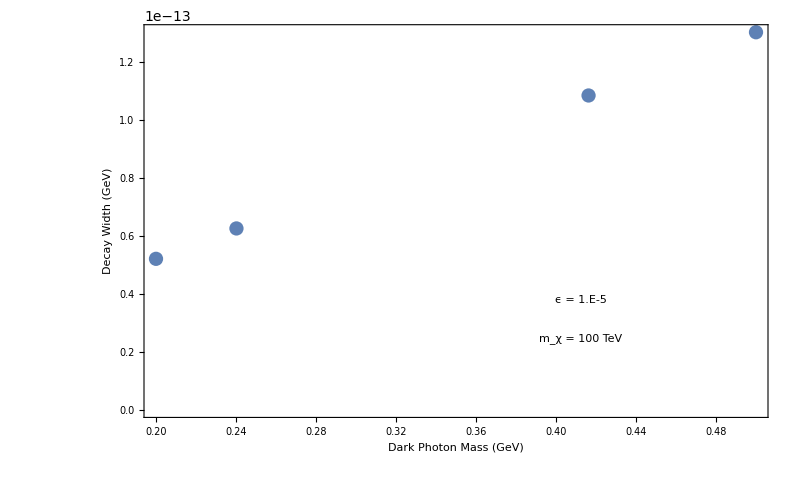

```mathematica
(*PLOTTING WIDTH*)
widthsimp=Flatten[Import[$widthsfile,"TSV"],1]//ToExpression
plottab=Table[{widthsimp⟦i,2⟧,widthsimp⟦i,5⟧},{i,1,Length[widthsimp]}];
(*Removes ones with failed widths:*)
Select[plottab,NumberQ[#⟦2⟧]==True&];
plottab⟦1,2⟧;
ListPlot[plottab,Frame->True,FrameLabel->{"Dark Photon Mass (GeV)","Decay Width (GeV)"},FrameStyle->Black,LabelStyle->25,ImageSize->800,Epilog->{Style[Text["ϵ = "<>ToString[ScientificForm[MGϵ,NumberFormat->(#1<>"E"<>#3&)]],Scaled[{0.7,0.3}]],20,Black],Style[Text["m_χ = "<>ToString[Round[DMmass/1000.]]<>" TeV",Scaled[{0.7,0.2}]],20,Black]}]
```

0.5

0.001

100.

2.

-3.

-0.25

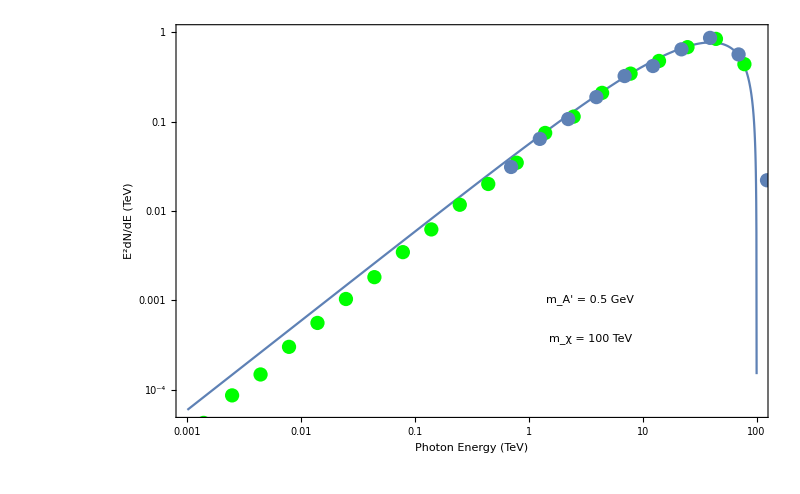

```mathematica
(*PLOTTING RAW SPECTRUM OUT OF PYTHIA AGAINST BOOSTED ANALYTICAL SPECTRUM*)
dNdx0a[x0_,ϵf_]:=(1/137.)/π(1+(1-x0)^2)/x0(Log[(4(1-x0))/ϵf^2]-1);
(*Boosting the spectrum:*)
dNdx1a[x1_,ϵ1_,ϵf_]:=(t1maxa=Min[1,(2x1)/ϵ1^2(1+√(1-ϵ1^2))];
t1mina=(2x1)/ϵ1^2(1-√(1-ϵ1^2));
2NIntegrate[1/(x0 √(1-ϵ1^2))dNdx0a[x0,ϵf],{x0,t1mina,t1maxa}])(*boosted photon spectrum for two mediators*);
dNdE1e[En_,mχ_,mA_]:=1/mχ dNdx1a[En/mχ,(2mA)/mχ,(2*0.511 10^-6(*TeV*))/mA];
(*SPECTRUM BEFORE ANY BOOST*)
runnumber=1;
photonErest=Flatten[Import[$pythonoutputfile<>StringTake[fn⟦runnumber⟧,-2],"TSV"]];
DPmass=DPmasstab⟦runnumber⟧
DMmassTeV=DMmass/1000.;
DPmassTeV=DPmass/1000.;
minbin=10^-5 DMmassTeV(*Min[photonErest]*)
maxbin=DMmassTeV
Log10[maxbin]
Log10[minbin]
nobins=20;
(Log10[minbin]-Log10[maxbin])/nobins
bins=Table[10^le,{le,Log10[minbin],Log10[maxbin],(Log10[maxbin]-Log10[minbin])/nobins}];

(*binned photon energies*)
bpe[spectrum_,bins_]:=(binnedE={};
Do[bin=Select[spectrum,bins⟦i⟧<#<bins⟦i+1⟧&];
binnedE=Append[binnedE,bin];
,{i,1,Length[bins]-1}];
binnedE)
(*Binned dN/dE from energies list. Returns list of {dNdE, Energy} in TeV*)
bdNdE[spectrum_,bins_]:=(binnedpe=bpe[spectrum,bins];
dNdElist={};
Do[
dN=Length[binnedpe⟦i⟧];
dE=bins⟦i+1⟧-bins⟦i⟧;
dNdEpoint={(bins⟦i+1⟧+bins⟦i⟧)/2,1/((*per annihilation*)nevents)dN/dE};
dNdElist=Append[dNdElist,dNdEpoint];
,{i,1,Length[binnedpe]}];
dNdElist
)
(*Binned E^2 dN/dE*)
bE2dNdE[spectrum_,bins_]:=(binnedpe=bpe[spectrum,bins];
dNdElist={};
Do[
dN=Length[binnedpe⟦i⟧];
dE=bins⟦i+1⟧-bins⟦i⟧;
dNdEpoint={(bins⟦i+1⟧+bins⟦i⟧)/2,((bins⟦i+1⟧+bins⟦i⟧)/2)^2 1/(2(*2 here because we have 2 mediators per event*)nevents)dN/dE};
dNdElist=Append[dNdElist,dNdEpoint];
,{i,1,Length[binnedpe]}];
dNdElist
)

(*Show[LogLogPlot[dNdE0a[en,DPmassTeV],{en,minbin,maxbin}],ListLogLogPlot[bdNdE[photonErest,bins],PlotStyle->Green],Frame->True,FrameLabel->{"Photon Energy (TeV)","dN/dE (TeV^-1)"},FrameStyle->Black,LabelStyle->25,ImageSize->800,Epilog->{Style[Text["m_A' = "<>ToString[DPmass]<>" GeV",Scaled[{0.5,0.2}]],20,Black]}]
*)
Show[LogLogPlot[en^2 dNdE1e[en,DMmassTeV,DPmassTeV],{en,minbin,maxbin}],ListLogLogPlot[bE2dNdE[photonErest,bins],PlotStyle->Green],ListLogLogPlot[qua],Frame->True,FrameLabel->{"Photon Energy (TeV)","E^2dN/dE (TeV)"},FrameStyle->Black,LabelStyle->25,ImageSize->800,Epilog->{Style[Text["m_A' = "<>ToString[DPmass]<>" GeV",Scaled[{0.7,0.3}]],20,Black],Style[Text["m_χ = "<>ToString[Round[DMmassTeV]]<>" TeV",Scaled[{0.7,0.2}]],20,Black]}]
```

```mathematica
bE2dNdE[photonErest,bins]
bins
```

{{0.00138914,0.0000423987},{0.00247028,0.0000861992},{0.00439285,0.000147798},{0.00781171,0.000301169},{0.0138914,0.000557877},{0.0247028,0.00103395},{0.0439285,0.00181513},{0.0781171,0.00345786},{0.138914,0.00621104},{0.247028,0.0117284},{0.439285,0.0200331},{0.781171,0.0346484},{1.38914,0.0746316},{2.47028,0.113756},{4.39285,0.209739},{7.81171,0.344392},{13.8914,0.477295},{24.7028,0.681216},{43.9285,0.842878},{78.1171,0.439205}}

{0.001,0.00177828,0.00316228,0.00562341,0.01,0.0177828,0.0316228,0.0562341,0.1,0.177828,0.316228,0.562341,1.,1.77828,3.16228,5.62341,10.,17.7828,31.6228,56.2341,100.}

```mathematica
ben
```

{0.5,0.894427,1.6,2.82843,5.,8.86002,15.7,28.0179,50.,88.8819,158.}